```mathematica
f[x_] = (Log2[x + 4])^((2x+5)^(1/3));
```

```mathematica
a = -1.3;
b = 3;
h = 0.2;
```

```mathematica
n=(b-a)/h;
```

```mathematica
pro1 [x_] = (f[x+h]-f[x-h])/(2h);
Table[{a+h*i,pro1[a+h*i]},{i,0,n}]
```

{{-1.3,1.02449},{-1.1,1.09966},{-0.9,1.1747},{-0.7,1.25042},{-0.5,1.32728},{-0.3,1.40558},{-0.1,1.48554},{0.1,1.5673},{0.3,1.65098},{0.5,1.73668},{0.7,1.82447}}

```mathematica
dif[x_]=D[f[x],x];
```

```mathematica
graphic1 = Plot[dif[x],{x,a,b},PlotRange->{{-2,3}, {0, 4}}];
graphic3 = ListPlot[Table[{a+h*i,dif[a+h*i]},{i,0,n}], PlotStyle->Red];
```

```mathematica
graphic2 = ListPlot[Table[{a+h*i,pro1[a+h*i]},{i,0,n}], PlotStyle->Green];
```

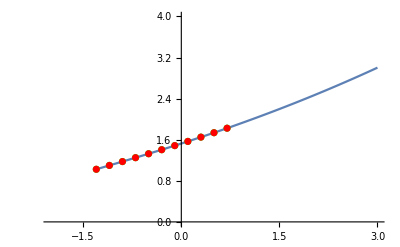

```mathematica
Show[graphic1, graphic2, graphic3]
```